#### Functions

```mathematica
Clear[makeLi]

makeLi[i_,parents_List,input_]:=Module[{num,den},If[i===input,
(*input node is left as a free variable*)
L[i],num=kf[i]+Total[Table[kf[i,p] L[p],{p,parents}]];
den=kt[i]+Total[Table[kt[i,p] L[p],{p,parents}]];
LT[i]*num/den]]

makeAllLi[g_Graph,input_]:=Association[Table[i->makeLi[i,VertexInComponent[g,i,{1}],input],{i,VertexList[g]}]]

expandLi[g_Graph,input_]:=Module[{defs,rules},defs=makeAllLi[g,input];
rules=Thread[L[#]->defs[#]&/@Keys[defs]];
FixedPoint[ReplaceAll[#,rules]&,defs]]


(*RandomDirectedGraphAdjacency[vertexCount_,edgeCount_]:=Module[{elems,adjacencyMatrix,graph},elems=RandomSample@PadRight[ConstantArray[1,edgeCount],vertexCount (vertexCount-1)/2];
adjacencyMatrix=Take[FoldList[RotateLeft,elems,Range[0,vertexCount-2]],All,vertexCount]~LowerTriangularize~-1;
adjacencyMatrix[[2,1]]=1;
adjacencyMatrix=Transpose[adjacencyMatrix];
graph=AdjacencyGraph[adjacencyMatrix]
(*<|"AdjacencyMatrix"->adjacencyMatrix,"Graph"->graph|>*)]*)

RandomDirectedGraphAdjacency[vertexCount_,edgeCount_,p_:0]:=Module[{elems,adjacencyMatrix,graph,backwardConnections,i,j},(*Original forward-only DAG construction*)elems=RandomSample@PadRight[ConstantArray[1,edgeCount],vertexCount (vertexCount-1)/2];
adjacencyMatrix=Take[FoldList[RotateLeft,elems,Range[0,vertexCount-2]],All,vertexCount]~LowerTriangularize~-1;
adjacencyMatrix[[2,1]]=1;
adjacencyMatrix=Transpose[adjacencyMatrix];
(*Add random backward connections with probability p*)If[p>0,
For[i=1,i<=vertexCount,i++,For[j=i+1,j<=vertexCount,j++,
(*Only add backward edge if there's no forward edge and random test passes*)
If[(*adjacencyMatrix[[i,j]]==0&&*)RandomReal[]<p,adjacencyMatrix[[j,i]]=1]]]];
graph=AdjacencyGraph[adjacencyMatrix]]


makeEquationSystem[g_Graph]:=Module[{nodes,eqns},nodes=VertexList[g];
eqns=Table[Module[{parents,num,den},parents=VertexInComponent[g,i,{1}];(*incoming neighbors*)
num=kf[i]+Total[Table[kf[i,p] L[p],{p,parents}]];
den=kt[i]+Total[Table[kt[i,p] L[p],{p,parents}]];
L[i]==LT[i]*num/den],{i,nodes}];
eqns]

makeEquationSystemRHS[g_Graph]:=Module[{nodes,eqns},nodes=VertexList[g];
eqns=Table[Module[{parents,num,den},parents=VertexInComponent[g,i,{1}];(*incoming neighbors*)num=kf[i]+Total[Table[kf[i,p] L[p],{p,parents}]];
den=kt[i]+Total[Table[kt[i,p] L[p],{p,parents}]];
LT[i]*num/den-L[i]],{i,nodes}];
eqns]

RandomKFKTParams[g_Graph,input_,dist_:{-1,1}]:=Module[{nodes,otherNodes,rules},nodes=VertexList[g];
otherNodes=DeleteCases[nodes,input];
rules=Flatten@Table[Module[{nbrs=VertexInComponent[g,node],kfVal,krVal},
kfVal=Exp[RandomReal[dist]];
krVal=Exp[RandomReal[dist]];
Join[{
kf[node]->kfVal,
kt[node]->kfVal+krVal},
Table[Module[{
kfij=Exp[RandomReal[dist]],
krij=Exp[RandomReal[dist]]},
{kf[node,nbr]->kfij,
kt[node,nbr]->kfij+krij}],{nbr,nbrs}]//Flatten]],{node,otherNodes}];
rules]


RandomLTParams[g_Graph,input_,dist_:{-1,1}]:=Module[{nodes,otherNodes,rules},nodes=VertexList[g];
otherNodes=DeleteCases[nodes,input];
rules=Flatten@Table[LT[node]->Exp[RandomReal[dist]],{node,otherNodes}];
rules]

CreateFeedforwardNNGraph[nodesPerLayer_List]:=Module[
{layers,nodes,edges,graph,maxNodes,yCoords,nodePos, cumCounts,idx},

layers=Length[nodesPerLayer];
maxNodes=Max[nodesPerLayer];

(*Maximum number of nodes in any layer*)(*Create a list of nodes*)
(*nodes=Flatten[Table[Table[Subscript[v,i,j],{j,nodesPerLayer[[i]]}],{i,layers}]];
edges=Flatten[Table[DirectedEdge[Subscript[v,i,j],Subscript[v,i+1,k]],{i,layers-1},{j,nodesPerLayer[[i]]},{k,nodesPerLayer[[i+1]]}]];*)

(*Flattened node list as L[1],L[2],...*)
nodes=Table[i,{i,Total[nodesPerLayer]}];
cumCounts=Prepend[Most@Accumulate[nodesPerLayer],0];
idx[i_,j_]:=cumCounts[[i]]+j;
edges=Flatten[Table[DirectedEdge[idx[i,j],idx[i+1,k]],{i,layers-1},{j,nodesPerLayer[[i]]},{k,nodesPerLayer[[i+1]]}]];

(*Calculate y-coordinates to center nodes in each layer*)
yCoords=0.75*Table[Range[-(nodesPerLayer[[i]]-1)/2,(nodesPerLayer[[i]]-1)/2],{i,layers}];
(*Combine x and y coordinates for node positions*)
nodePos=Flatten[Table[Table[{0.5*i,yCoords[[i,j]]},{j,Length[yCoords[[i]]]}],{i,layers}],1];
(*Create the graph*)graph=Graph[nodes,edges,VertexStyle->Black,EdgeStyle->Directive[Black,Thickness[0.005]],VertexCoordinates->AssociationThread[nodes->nodePos],VertexSize->0.15,ImageSize->160];
graph]

upstream[node_]:=Select[nodes,
(*exclude the node itself*)
#!=node&&GraphDistance[g,#,node]<∞&];
downstream[node_]:=Select[nodes,
(*exclude the node itself*)
#!=node&&GraphDistance[g,node,#]<∞&];

convertToNumDenom[x_]:=NumeratorDenominator[Together[x]]
```

#### Scans

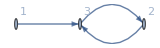

{-L[1]+(kf[1] LT[1])/kt[1],-L[3]+((kf[3]+kf[3,1] L[1]+kf[3,2] L[2]) LT[3])/(kt[3]+kt[3,1] L[1]+kt[3,2] L[2]),-L[2]+((kf[2]+kf[2,3] L[3]) LT[2])/(kt[2]+kt[2,3] L[3])}

```mathematica
(*layerList = {1,2,2,1};
nNodes = Total[layerList];
graph = CreateFeedforwardNNGraph[layerList];*)

graph=Graph[{1->3,2->3,3->2},VertexLabels->"Name"];
nNodes = 3;

(*SeedRandom[30];
nNodes = 3;
nEdges =4;
graph = RandomDirectedGraphAdjacency[nNodes,nEdges, 0.0];*)
(*coords=GraphEmbedding[graph];
graph = RandomDirectedGraphAdjacency[nNodes,nEdges, 0];*)

(*graph=RandomGraph[{nNodes,nEdges},DirectedEdges->True];*)

GraphPlot[graph,VertexLabels->Automatic]

eqs=makeEquationSystemRHS[graph]
```

```mathematica
makeEquationSystemRHS[g_Graph]:=Module[{nodes,eqns},
nodes=VertexList[g];
eqns=Table[Module[{parents,num,den},parents=VertexInComponent[g,i,{1}];
(*incoming neighbors*)
num=kf[i]+Total[Table[kf[i,p] L[p],{p,parents}]];
den=kt[i]+Total[Table[kt[i,p] L[p],{p,parents}]];
LT[i]*num/den-L[i]],{i,nodes}];
eqns]
```

```mathematica
num=kf[i]+Total[Table[kf[i,p] L[p],{p,{1,2}}]];
den=kt[i]+Total[Table[kt[i,p] L[p],{p,{1,2}}]];
D[LT[i]*num/den,L[1]]//Simplify
```

((-kt[i,1] (kf[i]+kf[i,2] L[2])+kf[i,1] (kt[i]+kt[i,2] L[2])) LT[i])/(kt[i]+kt[i,1] L[1]+kt[i,2] L[2])^2

```mathematica
eqs=makeEquationSystem[graph]
sol=Solve[eqs[[2;;nNodes]],Table[L[i],{i,2,nNodes}]]//Simplify;
(*L2expr=L[2]/.sol[[1]];
L3expr=L[3]/.sol[[1]];*)
expr = L[nNodes]/.sol[[2]];
allSimplePaths=FindPath[graph,1,nNodes,Infinity,All];
numberOfSimplePaths=Length[allSimplePaths]
(*num=D[L3expr,L[1]]//Simplify//Together//Numerator
Collect[num,L[1]]//TraditionalForm
CoefficientList[num,L[1]]//TraditionalForm*)
```

{L[1]==(kf[1] LT[1])/kt[1],L[3]==((kf[3]+kf[3,1] L[1]+kf[3,2] L[2]) LT[3])/(kt[3]+kt[3,1] L[1]+kt[3,2] L[2]),L[2]==((kf[2]+kf[2,3] L[3]) LT[2])/(kt[2]+kt[2,3] L[3])}

1

```mathematica
L2expr=L[2]/.sol[[2]]/.L[1]->0//Simplify
L3expr=L[3]/.sol[[2]]/.L[1]->0//Simplify
```

1/(2 (kt[2] kt[3,2]+kf[3,2] kt[2,3] LT[3]))(-kt[2] kt[3]+kf[2] kt[3,2] LT[2]-kf[3] kt[2,3] LT[3]+kf[2,3] kf[3,2] LT[2] LT[3]+√(4 (kf[3] kt[2]+kf[2] kf[3,2] LT[2]) (kt[3] kt[2,3]+kf[2,3] kt[3,2] LT[2]) LT[3]+(kt[2] kt[3]+kf[2] kt[3,2] LT[2]-(kf[3] kt[2,3]+kf[2,3] kf[3,2] LT[2]) LT[3])^2))

1/(2 (kt[3] kt[2,3]+kf[2,3] kt[3,2] LT[2]))(-kt[2] kt[3]-kf[2] kt[3,2] LT[2]+kf[3] kt[2,3] LT[3]+kf[2,3] kf[3,2] LT[2] LT[3]+√(4 (kf[3] kt[2]+kf[2] kf[3,2] LT[2]) (kt[3] kt[2,3]+kf[2,3] kt[3,2] LT[2]) LT[3]+(kt[2] kt[3]+kf[2] kt[3,2] LT[2]-(kf[3] kt[2,3]+kf[2,3] kf[3,2] LT[2]) LT[3])^2))

```mathematica
L3expr/L2expr//Simplify
```

((kt[2] kt[3,2]+kf[3,2] kt[2,3] LT[3]) (-kt[2] kt[3]-kf[2] kt[3,2] LT[2]+kf[3] kt[2,3] LT[3]+kf[2,3] kf[3,2] LT[2] LT[3]+√(4 (kf[3] kt[2]+kf[2] kf[3,2] LT[2]) (kt[3] kt[2,3]+kf[2,3] kt[3,2] LT[2]) LT[3]+(kt[2] kt[3]+kf[2] kt[3,2] LT[2]-(kf[3] kt[2,3]+kf[2,3] kf[3,2] LT[2]) LT[3])^2)))/((kt[3] kt[2,3]+kf[2,3] kt[3,2] LT[2]) (-kt[2] kt[3]+kf[2] kt[3,2] LT[2]-kf[3] kt[2,3] LT[3]+kf[2,3] kf[3,2] LT[2] LT[3]+√(4 (kf[3] kt[2]+kf[2] kf[3,2] LT[2]) (kt[3] kt[2,3]+kf[2,3] kt[3,2] LT[2]) LT[3]+(kt[2] kt[3]+kf[2] kt[3,2] LT[2]-(kf[3] kt[2,3]+kf[2,3] kf[3,2] LT[2]) LT[3])^2)))

```mathematica
D[expr,L[1]]//Simplify//TraditionalForm
```

1/(2 (LT(2) kf(2,3) kt(3,2)+L(1) kt(3,1) kt(2,3)+kt(3) kt(2,3))^2)(kt(2,3) kt(3,1) (-L(1) LT(3) kf(3,1) kt(2,3)+√((-LT(3) (L(1) kf(3,1) kt(2,3)+kf(3) kt(2,3)+LT(2) kf(2,3) kf(3,2))+kf(2) LT(2) kt(3,2)+kt(2) (L(1) kt(3,1)+kt(3)))^2+4 LT(3) (kt(2) L(1) kf(3,1)+kf(2) LT(2) kf(3,2)+kf(3) kt(2)) (LT(2) kf(2,3) kt(3,2)+L(1) kt(3,1) kt(2,3)+kt(3) kt(2,3)))+kf(2) LT(2) kt(3,2)-kf(3) LT(3) kt(2,3)-LT(2) LT(3) kf(2,3) kf(3,2)+kt(2) L(1) kt(3,1)+kt(2) kt(3))-(LT(2) kf(2,3) kt(3,2)+L(1) kt(3,1) kt(2,3)+kt(3) kt(2,3)) ((4 LT(3) kt(2,3) kt(3,1) (kt(2) L(1) kf(3,1)+kf(2) LT(2) kf(3,2)+kf(3) kt(2))+4 kt(2) LT(3) kf(3,1) (LT(2) kf(2,3) kt(3,2)+L(1) kt(3,1) kt(2,3)+kt(3) kt(2,3))+2 (kt(2) kt(3,1)-LT(3) kf(3,1) kt(2,3)) (-LT(3) (L(1) kf(3,1) kt(2,3)+kf(3) kt(2,3)+LT(2) kf(2,3) kf(3,2))+kf(2) LT(2) kt(3,2)+kt(2) (L(1) kt(3,1)+kt(3))))/(2 √((-LT(3) (L(1) kf(3,1) kt(2,3)+kf(3) kt(2,3)+LT(2) kf(2,3) kf(3,2))+kf(2) LT(2) kt(3,2)+kt(2) (L(1) kt(3,1)+kt(3)))^2+4 LT(3) (kt(2) L(1) kf(3,1)+kf(2) LT(2) kf(3,2)+kf(3) kt(2)) (LT(2) kf(2,3) kt(3,2)+L(1) kt(3,1) kt(2,3)+kt(3) kt(2,3))))-LT(3) kf(3,1) kt(2,3)+kt(2) kt(3,1)))

```mathematica
expr = expandLi[ graph,1][nNodes];
num = convertToNumDenom[expr][[1]];
num = convertToNumDenom[expr][[1]];
denom = convertToNumDenom[expr][[2]];
CoefficientList[num,L[1]]//Length
CoefficientList[denom,L[1]]//Length

allSimplePaths=FindPath[graph,1,nNodes,Infinity,All];
numberOfSimplePaths=Length[allSimplePaths]
```

2

2

1

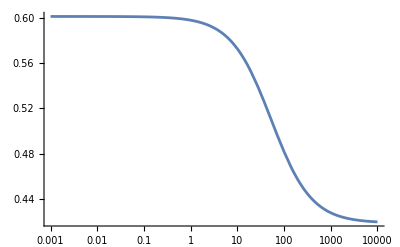

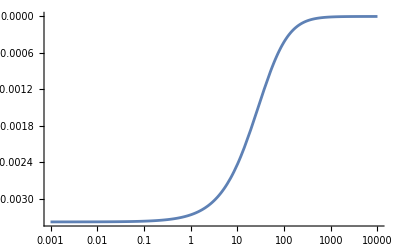

```mathematica
kfktRules=RandomKFKTParams[graph,1,{-1,4}];
ltRules=RandomLTParams[graph,1,{-1,4}];
allRules=Join[kfktRules,ltRules];

rhs = makeEquationSystemRHS[graph][[2;;]]/.allRules;

lower = 10^-3;
upper = 10^4;
L1Array = PowerRange[lower,upper,1.1];

(*LVars = Table[L[i],{i,1,nNodes}];
sols = Table[LVars[[2;;]]/.FindRoot[rhs/.L[1]->L1Array[[m]],Table[{LVars[[i]],LT[i]/.ltRules},{i,2,nNodes}],AccuracyGoal->10,PrecisionGoal->10],{m,1,Length[L1Array]}];
solFunc:=Interpolation[Transpose[{L1Array,sols[[;;,nNodes-1]]}]]*)

solFuncc[r_]:=Evaluate[expr/.allRules/.L[1]->r];
gradFunc = solFuncc';
LogLinearPlot[solFuncc[r],{r,lower,upper},PlotRange->Full]
LogLinearPlot[gradFunc[r],{r,lower,upper},PlotRange->Full]
```

```mathematica
(*layerList = {1,2,1};
nNodes = Total[layerList];
graph = CreateFeedforwardNNGraph[layerList]*)
SeedRandom[34];
expr = L[nNodes]/.sol[[2]];
lower = 10^-3;
upper = 10^3;
nPoints = 200;

L1Array = PowerRange[lower,upper,1.1];
samplePts=Table[10^r,{r,Log10[1.01lower],Log10[0.99upper],(Log10[upper]-Log10[lower])/nPoints}]//N;

signChangesList = {};

Do[

kfktRules=RandomKFKTParams[graph,1,{-4,4}];
     ltRules=RandomLTParams[graph,1,{-4,4}];
allRules=Join[kfktRules,ltRules];

(*rhs = makeEquationSystemRHS[graph][[2;;]]/.allRules;
LVars = Table[L[i],{i,1,nNodes}];
sols = Table[LVars[[2;;]]/.FindRoot[rhs/.L[1]->L1Array[[m]],Table[{LVars[[i]],LT[i]/.ltRules},{i,2,nNodes}],AccuracyGoal->10,PrecisionGoal->10,MaxIterations->5000,Method->{"Newton", "StepControl" -> "TrustRegion"}],{m,1,Length[L1Array]}];

solFunc:=Interpolation[Transpose[{L1Array,sols[[;;,nNodes-1]]}]];
gradFunc = solFunc';*)

     solFuncc[r_]:=Evaluate[expr/.allRules/.L[1]->r];
gradFunc=solFuncc';

  signChanges=Partition[samplePts,2,1]/. {a_,b_}:>If[Sign[gradFunc[a]]!=Sign[gradFunc[b]],{a,b},Nothing];

AppendTo[signChangesList,Length[signChanges]];
,{nIter,1,10000}
]//AbsoluteTiming
```

{43.2864,Null}

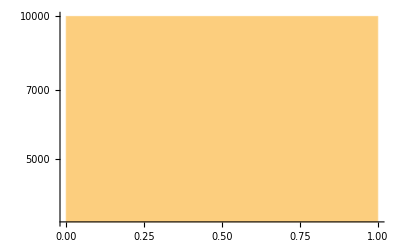

0

```mathematica
Histogram[signChangesList,ScalingFunctions->{None,"Log"}]
Max[signChangesList]
```

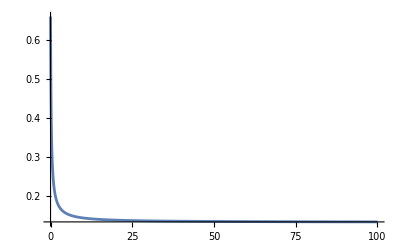

```mathematica
Plot[solFuncc[r],{r,0,100},PlotRange->Full]
```

```mathematica
Together[expr]
```

$Aborted

```mathematica
num
```

```mathematica
signChangesList
```

{0,0,0,0,0,0,0,0,0,0}